# CRMSD and D

## data loading

```mathematica
p0s={3.9,3.85,3.825,3.80,3.775,3.75};
```

```mathematica
temperatures={{0.039,0.01,0.005,0.002,0.001,0.0005,0.00033,0.00014,0.000091,0.000077,0.000054,0.000045,0.000036},{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.03105, 0.025 ,0.02 ,0.016 ,0.012, 0.01, 0.009 ,0.008 ,0.0075, 0.007 ,0.0063, 0.0056 ,0.0054},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{10, 19, 9,9,46.2416,35.0693,135.321,564.239,829.48,897.484,1365.27,1522.57,3000},{2, 4,10, 20, 40,60, 80, 200, 500, 800, 1400, 2500, 4200,5000, 6000, 8500, 9500},{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{2, 10,20 ,30, 80 ,100 ,400 ,500 ,2500 ,2500, 3000 ,7000, 10000},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}};
```

```mathematica
orientationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/orientationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
orientationalsReal[[2,14]]
```

Table[DeleteCases[Table[orientationals⟦p,T,i,1,rec⟧,{i,Length[orientationals⟦p,T⟧]}],_Missing|_Part],{rec,-∞}]

```mathematica
translationals=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/translationReIm_N4096_p","_T","_",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],records[[p,i]]},{3,3,8,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::format: Cannot import data as Data.

General::stop: Further output of Import::format will be suppressed during this calculation.

```mathematica
Normal[sigmaXXsigmaYYs[[1,1,1,1]]]
```

{0.251468,0.244393,0.247302,0.238019,0.246261,0.247319,0.239919,0.244294,0.243343,0.242202,0.242348}

```mathematica
Flatten[{{{1,2},2,{{2,1}}}}]
```

{1,2,2,2,1}

```mathematica
orientationals[[2,14]]
```

{}

```mathematica
Table[Table[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,10,11,10,11},{11,11,11,11,11,11,8,11,11,11}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{3,5,5,3,1,4,4,4,3,3},{2,3,3,3,3,1,2,1,1,1}},{{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,7,8,11,11,11,11,11},{11,5,11,4,4,10,9},{4,5,4,5,1,5,5,1},{1,2,3,2,2,2,2,3}},{{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11}},{{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11},{11,11,11,11,11,11,11,11,11},{1,2,5,1,5,5,1,6},{2,2,2,2,2,3,2}}}

```mathematica
orientationalsReal=Table[Table[Flatten[Table[DeleteCases[Table[orientationals[[p,T,i,1,rec]],{i,Length[orientationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
orientationalsIm=Table[Table[Flatten[Table[DeleteCases[Table[orientationals[[p,T,i,2,rec]],{i,Length[orientationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[orientationals[[p,T,i,1]]],{i,Length[orientationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
VarOri=Table[Table[Variance[Table[Sqrt[orientationalsIm[[p,T,rec]]^2+orientationalsReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.000024906,0.0000237851,0.0000249544,0.0000263616,0.0000330017,0.0000222213,0.0000253206,0.0000260771,0.0000233739,0.0000260104,0.0000220208,0.0000245192,0.0000239637},{0.0000301701,0.0000468281,0.0000683461,0.0000599482,0.000091052,0.000100472,0.00012323,0.000110957,0.000118597,0.000113957,0.000124039,0.000118636,0.000142498,0.000134309,0.000182314,0.000124635,0.000251869},{0.0000249455,0.0000340848,0.00005006,0.0000590883,0.0000949429,0.000120529,0.000183249,0.000227236,0.00025026,0.000362483,0.000466289,0.000504535,0.00105208,0.00270169,0.00297227,0.000608696},{0.0000410703,0.0000389916,0.0000561167,0.0000769108,0.000109169,0.000241223,0.000442681,0.00084194,0.00225557,0.0048254,0.0015261,0.000614719,0.000197638,0.000118758},{0.0000790313,0.000118981,0.000143367,0.000284167,0.000816288,0.00249779,0.00385576,0.00166658,0.00172543,0.000685225,0.00019879,0.000115117,0.000087578},{0.0000423592,0.0000739827,0.000118068,0.000157976,0.000388524,0.000872396,0.0038062,0.00134818,0.000352668,0.000195169,0.0000490992}}

```mathematica
VarOri={{0.00002490601288754374,0.00002378508480613404,0.000024954442369584887,0.000026361557185598035,0.00003300166879753895,0.000022221321498995472,0.00002532059872829892,0.00002607711558997636,0.000023373946797499805,0.00002601042445650548,0.000022020766338925703,0.000024519207764839845,0.000023963706478320727},{0.000030170127368511545,0.00004682811941991142,0.0000683461307724868,0.00005994816082061668,0.00009105200929795181,0.0001004717958929182,0.00012323036155322412,0.0001109566205825853,0.00011859659570477375,0.0001139566666590226,0.00012403910149768075,0.00011863632079133343,0.00014249777766077695,0.00013430890838979413,0.0001823136067554804,0.00012463535868512043,0.0002518691357485699},{0.000024945526265102764,0.000034084769900379785,0.00005006004641255978,0.00005908825444773038,0.00009494288637769288,0.00012052869121643638,0.00018324931803017462,0.0002272355993744432,0.00025025955132281614,0.00036248332679778467,0.00046628876004650884,0.0005045347487073952,0.0010520759200326692,0.002701690302604771,0.002972265826221556,0.0006086959742373482},{0.00004107033841807075,0.00003899163216017076,0.000056116736513896545,0.00007691082577923393,0.00010916909292506406,0.0002412229221668894,0.0004426811160647321,0.0008419399340510113,0.0022555747897636757,0.004825395685005659,0.0015260994820706251,0.0006147192656147226,0.0001976380733507302,0.00011875791896913328},{0.00007903125687632536,0.00011898060155977387,0.00014336727899491087,0.0002841665702758021,0.0008162878954123455,0.002497785375995761,0.003855756592482135,0.0016665779964660033,0.0017254258833198628,0.0006852254133230685,0.0001987898073712529,0.00011511724064827518,0.00008757799764393955},{0.00004235916368896955,0.00007398274697888933,0.00011806839746533585,0.00015797553028527284,0.00038852405663309736,0.0008723957160903758,0.0038062004242061438,0.0013481788433104356,0.0003526677720484125,0.000195169258659632,0.00004909923154704943}};
```

```mathematica
VarOri={{0.000030170127368511545,0.00004682811941991142,0.0000683461307724868,0.00005994816082061668,0.00009105200929795181,0.0001004717958929182,0.00012323036155322412,0.0001109566205825853,0.00011859659570477375,0.0001139566666590226,0.00012403910149768075,0.00011863632079133343,0.00014249777766077695,0.00013430890838979413,0.0001823136067554804,0.00012463535868512043,0.0002518691357485699},{0.000024945526265102764,0.000034084769900379785,0.00005006004641255978,0.00005908825444773038,0.00009494288637769288,0.00012052869121643638,0.00018324931803017462,0.0002272355993744432,0.00025025955132281614,0.00036248332679778467,0.00046628876004650884,0.0005045347487073952,0.0010520759200326692,0.002701690302604771,0.002972265826221556,0.0006086959742373482},{0.00004107033841807075,0.00003899163216017076,0.000056116736513896545,0.00007691082577923393,0.00010916909292506406,0.0002412229221668894,0.0004426811160647321,0.0008419399340510113,0.0022555747897636757,0.004825395685005659,0.0015260994820706251,0.0006147192656147226,0.0001976380733507302,0.00011875791896913328},{0.00007903125687632536,0.00011898060155977387,0.00014336727899491087,0.0002841665702758021,0.0008162878954123455,0.002497785375995761,0.003855756592482135,0.0016665779964660033,0.0017254258833198628,0.0006852254133230685,0.0001987898073712529,0.00011511724064827518,0.00008757799764393955},{0.00004235916368896955,0.00007398274697888933,0.00011806839746533585,0.00015797553028527284,0.00038852405663309736,0.0008723957160903758,0.0038062004242061438,0.0013481788433104356,0.0003526677720484125,0.000195169258659632,0.00004909923154704943}};
```

```mathematica
translationalReal=Table[Table[Flatten[Table[DeleteCases[Table[translationals[[p,T,i,1,rec]],{i,Length[translationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[translationals[[p,T,i,1]]],{i,Length[translationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
translationalIm=Table[Table[Flatten[Table[DeleteCases[Table[translationals[[p,T,i,2,rec]],{i,Length[translationals[[p,T]]]}],_Missing|_Part],{rec,Max[Table[Length[translationals[[p,T,i,1]]],{i,Length[translationals[[p,T]]]}]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 11 of … does not exist.

Part::partw: Part 9 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
VarTrans=Table[Table[Variance[Table[Sqrt[translationalIm[[p,T,rec]]^2+translationalReal[[p,T,rec]]^2],{rec,Length[orientationalsIm[[p,T]]]}]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.0000485809,0.0000886895,0.0000646971,0.0000574927,0.000084147,0.0000534879,0.000073723,0.000115838,0.0000693644,0.0000589085,0.0000953976,0.0000617995,0.0000642567},{0.0000514885,0.0000723372,0.0000998845,0.000118544,0.00010094,0.00011182,0.000107955,0.000120259,0.000140906,0.000119204,0.000111151,0.000154206,0.000171507,0.000095929,0.000115839,0.000150025,0.000128151},{0.0000740906,0.0000910399,0.0000833416,0.000118127,0.00011846,0.000127165,0.000122982,0.000116032,0.000136256,0.000137062,0.000128482,0.000124591,0.000127215,0.000162129,0.000111069,0.000711172},{0.0000722533,0.0000800723,0.000118029,0.0000816652,0.000100038,0.000158919,0.00016646,0.000161923,0.000205021,0.000198996,0.000425862,0.00012176,0.000889531,0.000339863},{0.000102714,0.000112271,0.000114196,0.000124635,0.000165866,0.000200528,0.000187505,0.000298548,0.00065653,0.000673561,0.00178496,0.0013694,0.00273007},{0.0000759618,0.0000924791,0.0000999969,0.000100554,0.000155772,0.000192148,0.000292931,0.000870244,0.000104221,0.000473715,0.000122538}}

```mathematica
VarTrans={{0.00005148852053879982,0.00007233720709410422,0.00009988445954472588,0.0001185438087749257,0.00010094032940562058,0.0001118196684912823,0.00010795526062763165,0.00012025886778494213,0.00014090593491466612,0.00011920360304475908,0.00011115086722625884,0.00015420566239037614,0.00017150694875179374,0.00009592897666868082,0.00011583946366132854,0.0001500254694910231,0.0001281510514897041},{0.00007409059227211154,0.00009103993709224762,0.00008334156183388549,0.00011812710842371973,0.00011846029472960335,0.00012716545177716913,0.00012298159062440863,0.00011603198878168445,0.00013625580162554812,0.00013706212281812307,0.00012848163112755045,0.0001245911502900826,0.00012721508349541828,0.00016212935433965067,0.00011106934973927036,0.0007111722858044473},{0.00007225328833142457,0.00008007228513783775,0.00011802850268435936,0.00008166524886996393,0.00010003831262982861,0.0001589190710756473,0.00016646046969866996,0.00016192302373568192,0.00020502149448020152,0.00019899605433503756,0.00042586190038728907,0.00012175952885309977,0.0008895308104305083,0.0003398626373772594},{0.00010271445948898944,0.00011227146465006252,0.00011419591505619976,0.00012463466549795415,0.00016586644344294052,0.00020052848550648758,0.00018750512178581874,0.0002985479252258541,0.0006565297553460423,0.0006735607448836298,0.001784960928691206,0.0013694040068500048,0.002730072449859463},{0.00007596175538292422,0.00009247908449554139,0.00009999694251173306,0.00010055417112910885,0.00015577168689191707,0.0001921481151981721,0.00029293130116893036,0.0008702439447708078,0.00010422083172796913,0.000473714969977173,0.00012253827526514328}};
```

```mathematica
χ
```

## Plots and fitting

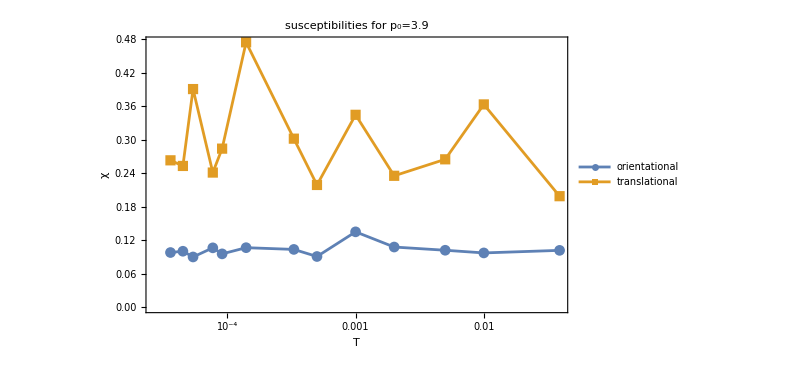
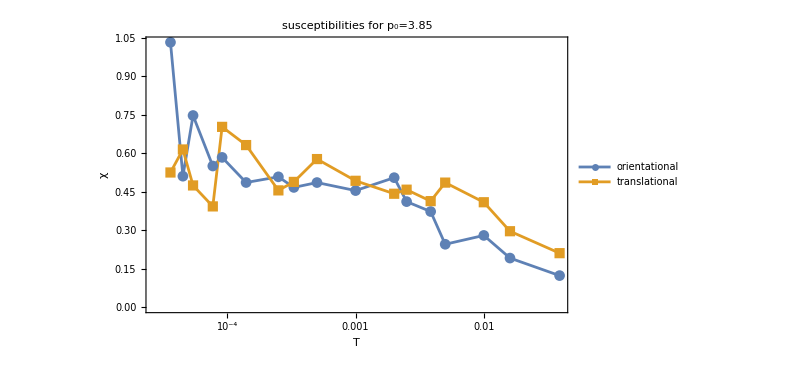
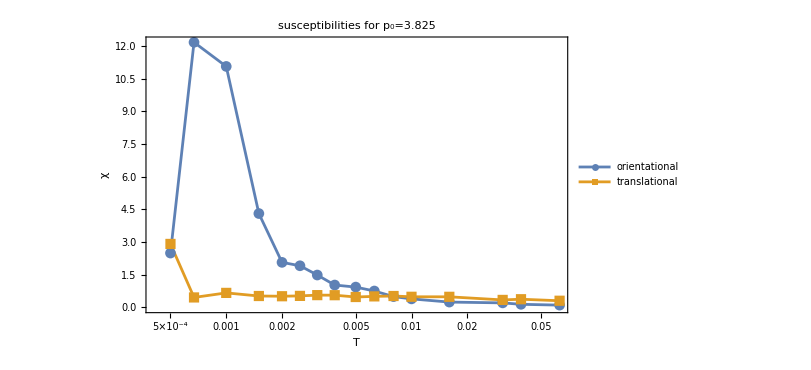
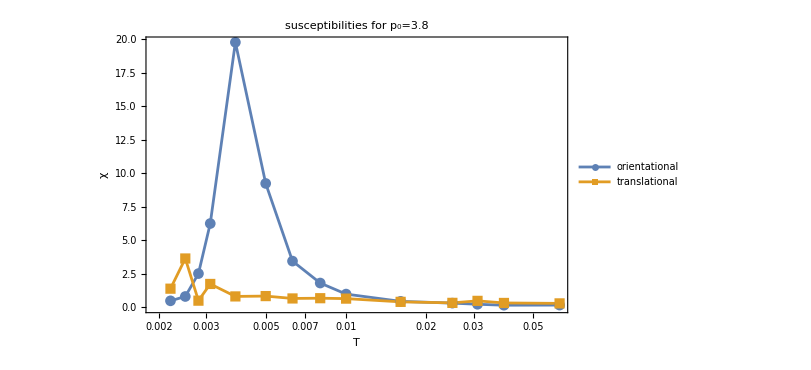
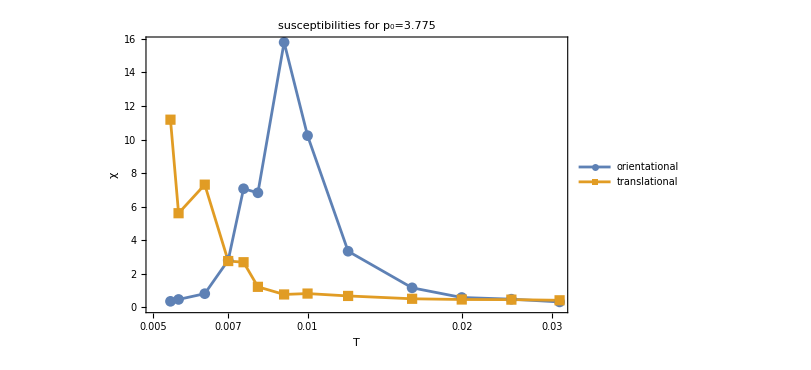
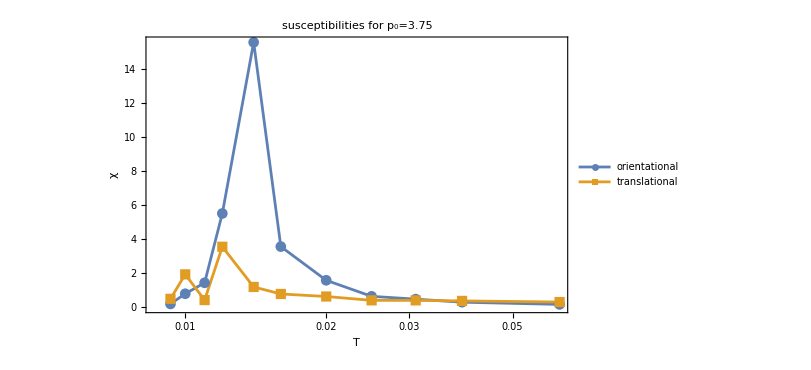

```mathematica
orderparameter=Table[ListLogLinearPlot[{Table[{temperatures[[p,T]],4096*VarOri[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{temperatures[[p,T]],4096*VarTrans[[p,T]]},{T,Length[temperatures[[p]]]}]},PlotLegends->{"orientational","translational"},PlotStyle->Automatic,FrameLabel->{"T","χ"},ImageSize->600,PlotLabel->"susceptibilities for p_0="<>ToString[p0s[[p]]],Joined->True,PlotRange->All,PlotMarkers->Automatic],{p,Length[p0s]}]
```

```mathematica
Table[Export["/home/chengling/Research/updates/04112024/orderPa"<>ToString[p0s[[p]]]<>".jpeg",orderparameter[[p]],ImageResolution->600],{p,Length[p0s]}]
```

{/home/chengling/Research/updates/04112024/orderPa3.85.jpeg,/home/chengling/Research/updates/04112024/orderPa3.825.jpeg,/home/chengling/Research/updates/04112024/orderPa3.8.jpeg,/home/chengling/Research/updates/04112024/orderPa3.775.jpeg,/home/chengling/Research/updates/04112024/orderPa3.75.jpeg}

```mathematica
chiOrderTable=Table[Prepend[Table[{temperatures[[p,T]],VarOri[[p,T]]*4096,VarTrans[[p,T]]*4096},{T,Length[temperatures[[p]]]}],{"T","Orientational susceptibility","Translational susceptibility"}],{p,Length[p0s]}]
```

{{{T,Orientational susceptibility,Translational susceptibility},{0.039,0.102015,0.198987},{0.01,0.0974237,0.363272},{0.005,0.102213,0.264999},{0.002,0.107977,0.23549},{0.001,0.135175,0.344666},{0.0005,0.0910185,0.219086},{0.00033,0.103713,0.30197},{0.00014,0.106812,0.474474},{0.000091,0.0957397,0.284116},{0.000077,0.106539,0.241289},{0.000054,0.0901971,0.390749},{0.000045,0.100431,0.253131},{0.000036,0.0981553,0.263195}},{{T,Orientational susceptibility,Translational susceptibility},{0.039,0.123577,0.210897},{0.016,0.191808,0.296293},{0.01,0.279946,0.409127},{0.005,0.245548,0.485555},{0.00385,0.372949,0.413452},{0.0025,0.411532,0.458013},{0.002,0.504752,0.442185},{0.001,0.454478,0.49258},{0.0005,0.485772,0.577151},{0.00033,0.466767,0.488258},{0.00025,0.508064,0.455274},{0.00014,0.485934,0.631626},{0.000091,0.583671,0.702492},{0.000077,0.550129,0.392925},{0.000054,0.746757,0.474478},{0.000045,0.510506,0.614504},{0.000036,1.03166,0.524907}},{{T,Orientational susceptibility,Translational susceptibility},{0.063,0.102177,0.303475},{0.039,0.139611,0.3729},{0.03105,0.205046,0.341367},{0.016,0.242025,0.483849},{0.01,0.388886,0.485213},{0.008,0.493686,0.52087},{0.0063,0.750589,0.503733},{0.005,0.930757,0.475267},{0.00385,1.02506,0.558104},{0.0031,1.48473,0.561406},{0.0025,1.90992,0.526261},{0.002,2.06657,0.510325},{0.0015,4.3093,0.521073},{0.001,11.0661,0.664082},{0.00067,12.1744,0.45494},{0.0005,2.49322,2.91296}},{{T,Orientational susceptibility,Translational susceptibility},{0.063,0.168224,0.295949},{0.039,0.15971,0.327976},{0.03105,0.229854,0.483445},{0.025,0.315027,0.334501},{0.016,0.447157,0.409757},{0.01,0.988049,0.650933},{0.008,1.81322,0.681822},{0.0063,3.44859,0.663237},{0.005,9.23883,0.839768},{0.00385,19.7648,0.815088},{0.0031,6.2509,1.74433},{0.0028,2.51789,0.498727},{0.0025,0.809526,3.64352},{0.0022,0.486432,1.39208}},{{T,Orientational susceptibility,Translational susceptibility},{0.03105,0.323712,0.420718},{0.025,0.487345,0.459864},{0.02,0.587232,0.467746},{0.016,1.16395,0.510504},{0.012,3.34352,0.679389},{0.01,10.2309,0.821365},{0.009,15.7932,0.768021},{0.008,6.8263,1.22285},{0.0075,7.06734,2.68915},{0.007,2.80668,2.7589},{0.0063,0.814243,7.3112},{0.0056,0.47152,5.60908},{0.0054,0.358719,11.1824}},{{T,Orientational susceptibility,Translational susceptibility},{0.063,0.173503,0.311139},{0.039,0.303033,0.378794},{0.03105,0.483608,0.409587},{0.025,0.647068,0.41187},{0.02,1.59139,0.638041},{0.016,3.57333,0.787039},{0.014,15.5902,1.19985},{0.012,5.52214,3.56452},{0.011,1.44453,0.426889},{0.01,0.799413,1.94034},{0.0093,0.20111,0.501917}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",chiOrderTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.900.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.775.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/orderParameterSusceptibilityP3.750.csv}